### Aufgabe 2.1.1

```mathematica
f[x_]:=5*E^(-(x-8)^2)+2
```

```mathematica
f[0]
```

2+5/ⅇ^64

```mathematica
f[10]
```

2+5/ⅇ^4

### Aufgabe 2.1.2

```mathematica
Manipulate[Plot[a*E^(-(x-b)^2)+2,{x,-10,10}],{a,1,5},{b,2,8}]
```

Der Parameter a beschreibt die Hoehe des Hochpunktes der Funktion. Der Parameter b beschreibt die Verschiebung des Hochpunktes auf der X-Achse.

### Aufgabe 2.1.3

```mathematica
f1[a_,b_,x_]:=a*E^(-(x-b)^2)+2
```

```mathematica
Solve[f1'[x]==0]
```

{{f1'[x]→0}}

```mathematica
f''[0,b,x]
```

1270/ⅇ^64

```mathematica
f''[a,b,b]
```

-10 ⅇ^(-(-8+a)^2)+20 (-8+a)^2 ⅇ^(-(-8+a)^2)

```mathematica
f[a,b,b]
```

f[a,b,b]

### Aufgabe 2.1.4

```mathematica
Solve[f1''[x]==0]
```

{{f1''[x]→0}}

```mathematica
Simplify[f1'''[-0.7071067811865475+b]]
```

f1^(3)[-0.707107+b]

```mathematica
Simplify[f1'''[-0.7071067811865475+b]]
```

f1^(3)[-0.707107+b]

```mathematica
f1[-0.7071067811865475+b]
```

f1[-0.707107+b]

```mathematica
f1[0.7071067811865475+b]
```

f1[0.707107+b]

```mathematica
0.7071067811865475+b-(-0.7071067811865475+b)
```

1.41421

### Aufgabe 2.2.1

```mathematica
g[x_]:=0.5*x+1
```

```mathematica
Pfad[x_]:=a*x^6+b*x^5+c*x^4+d*x^3+f*x^2+g*x+h
```

```mathematica
Solve[Pfad'[5]==0&&Pfad[5]==1&&Pfad[10]==6&&Pfad[0]==1&&g'[0]==0.5&&g''[0]==0&&g'[10]==0.5]
```

{{d→1/50-3250 a-275 b-20 c,f→-1/5+29375 a+2250 b+125 c,g→1/2-68750 a-5000 b-250 c,h→1}}

### Aufgabe 2.2.2

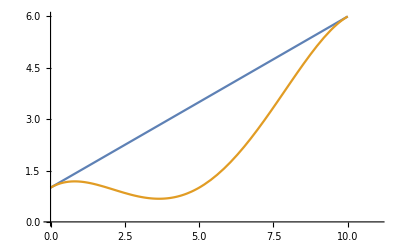

```mathematica
p2[x_]:=-0.004 x^4+0.08 x^3-0.4 x^2+0.5 x+1
Plot[{g[x],p2[x]},{x,0,11},PlotRange->{0,6}]
```

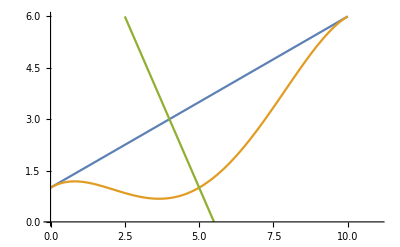

```mathematica
HT[x_]:=-2 x+11
Plot[{g[x],p2[x],HT[x]},{x,0,11},PlotRange->{0,6}]
```

```mathematica
Solve[HT[x]==p2[x]]
```

{{x→-0.236379-5.6797 ⅈ},{x→-0.236379+5.6797 ⅈ},{x→5.},{x→15.4728}}

```mathematica
Solve[HT[x]==g[x]]
```

{{x→4.}}

```mathematica
Integrate[g[x],{x,4,10}]-Integrate[p2[x],{x,5,10}]
```

9.91667

### Aufgabe 3.1.1

```mathematica
Probability[X==2,X\[Distributed]BinomialDistribution[27,0.03]]
```

0.147517

### Aufgabe 3.1.2

```mathematica
Reduce[Probability[X>=2,X\[Distributed]BinomialDistribution[n,0.03]]>=0.5]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::fexp: Warning: Reduce used FunctionExpand to transform the system. Since FunctionExpand transformation rules are only generically correct, the solution set might have been altered.

(Beta[0.03,2,-1+n]|Gamma[-1+n]|Gamma[1+n])∈ℝ&&n≥55.605

```mathematica
Probability[X>=2,X\[Distributed]BinomialDistribution[56,0.03]]
```

0.503761

### Aufgabe 3.2.2

```mathematica
0.74*0.01
```

0.0074

Antwort: A und F sind stochastisch nicht unabhängig voneinander.

### Aufgabe 3.2.3

```mathematica
0.7335/0.74
```

0.991216

```mathematica
0.2565/0.26
```

0.986538

Antwort: Androids sind minimal besser

### Aufgabe 3.3

```mathematica
N[Probability[X==0,X\[Distributed]BinomialDistribution[5,(3/75)]]]
```

0.815373

```mathematica
N[Probability[X==3,X\[Distributed]BinomialDistribution[5,(3/75)]]]
```

0.000589824

### Aufgabe 3.4.2

```mathematica
StandardDeviation[BinomialDistribution[100,0.86]]
```

3.46987

### Aufgabe 3.4.3

H0 : Die Wahrscheinlichkeit ist kleiner geworden p_0 < 5%

H1 : Die Wahrscheinlichkeit ist größer geworden p_ 0 > 5 %

### Aufgabe 4.1.2

```mathematica
gScott[s_]:={500,2000,2400}+s*{-1,-2,-1}
```

```mathematica
Felswand[u_,v_]:={300,400,0}+u*({300,400,0}-{-700,800,0})+v*({300,400,0}-{-200,600,2500})
```

```mathematica
{300,400,0}-{-700,800,0}
```

{1000,-400,0}

```mathematica
Solve[gScott[s]==Felswand[u,v]]
```

{{s→700,u→-4/25,v→-17/25}}

```mathematica
gScott[700]
```

{-200,600,1700}

### Aufgabe 4.2.1

```mathematica
{-60,-20,5}-{-20,80,0}
```

{-40,-100,5}

```mathematica
SichtVonKrel[t_]:={-60,-20,5}+t*{-40,-100,5}
```

```mathematica
U[r_,u_]
```